```mathematica
(* Classical Theory for Black Body Radiation *)
```

```mathematica
k= 1.23*10^-23; T=600;λ=500;
```

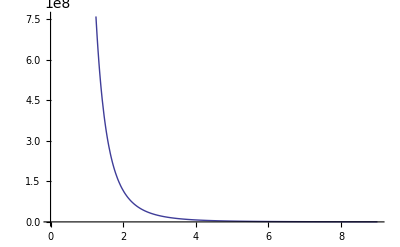

```mathematica
Plot[8*Pi*k*T/((λ)^4),{λ,0,900*10^-9}]
```

```mathematica
Animate[Plot[8*Pi*k*T/((λ)^4),{λ,0,900*10^-9}],{T,500,5000},AnimationRunning ->False]
```

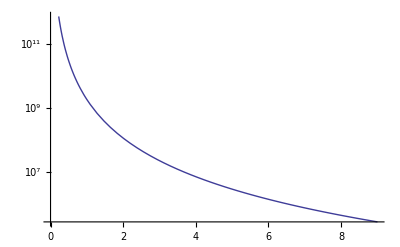

```mathematica
LogPlot[8*Pi*k*T/((λ)^4),{λ,0,900*10^-9}]
```

```mathematica
ClassicBB:=8*Pi*k*T/(λ)^4
```

```mathematica
T
```

10000

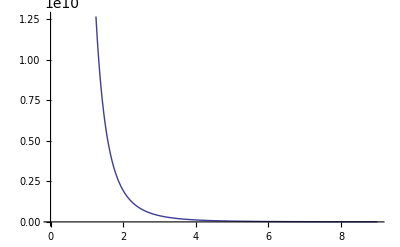

```mathematica
Plot[ClassicBB,{λ,0,900*10^-9}]
```

```mathematica
Plot3D[ClassicBB,{λ,0,900*10^-9},{T,500,5000}]
```

-Graphics3D-

```mathematica
Animate[Plot[ClassicBB,{λ,0,900*10^-9}],{T,500,5000},AnimationRunning ->False]
```

```mathematica
(*
Planck/Einstein Quantized Version of Black Boday Radiation 
*)
```

```mathematica
k= 1.23*10^-23; T=100;lamda=400;
```

```mathematica
c= 3.0*10^8; h=6.62*10^-34;
```

```mathematica
(* Note converted m to nm in equation so that scale was in nm *)
```

```mathematica
Plot3D[8*Pi*h*c/( ((λ*10^-9)^5)*(Exp[(h*c/(k*T*λ*10^-9))]-1)),{T,100,500},{λ,20000, 0.0},AxesLabel->{Temp, Wavlength }, PlotRange->Full]
```

-Graphics3D-

```mathematica
T=10000
```

10000

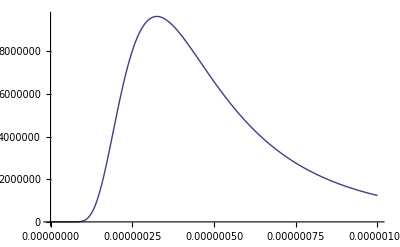

```mathematica
Plot[8*Pi*h*c/( (λ^5)*(Exp[(h*c/(k*T*λ))]-1)),{λ,0.0, 1000*10^-9}]
```

```mathematica
Animate[Plot[8*Pi*h*c/( (λ^5)*(Exp[(h*c/(k*T*λ))]-1)),{λ,0.0, 3000*10^-9}],{T,1000,10000},AnimationRunning ->False]
```

```mathematica
PlanckBB:= 8*Pi*h*c/( (λ^5)*(Exp[(h*c/(k*T*λ))]-1))
```

```mathematica
(*  Unable to put Generalized function into Animate although goes into Plot fine   ??*)
```

```mathematica
Animate[Plot[PlanckBB,{λ,0.0, 3000*10^-9}],{T,1000,10000},AnimationRunning ->False]
```